## Readme

Author: Victor Gitton

This is the notebook accompanying the article “Symmetric Local Distributions and Bell Inequalities in the Triangle Network”.

It is recommended to start looking at the notebook without evaluating anything, since all the cells already display their outputs, and some cells take a while to evaluate.

To run the notebook: first evaluate the cells of the “Utilities” section. Alternatively, use Evaluation > Evaluate Initialization Cells. Then, can run the individual cells that confirm the findings related to the different figures of the article.

## Utilities

```mathematica
colorsPerOutcome={RGBColor["#010475"],RGBColor["#A60167"],RGBColor["#F59A25"],RGBColor["#017455"]}
```

{RGBColor[0.00392156862745098, 0.01568627450980392, 0.4588235294117647],RGBColor[0.6509803921568628, 0.00392156862745098, 0.403921568627451],RGBColor[0.9607843137254902, 0.6039215686274509, 0.1450980392156863],RGBColor[0.00392156862745098, 0.4549019607843137, 0.3333333333333333]}

### Flags

```mathematica
(*Maps a set of subflags to something that looks like a flag*)
subflagsToFlag[subflags_,n_]:=Indexed[subflags,{1+IntegerPart[n*#1],1+IntegerPart[n*#2]}][n*#1-IntegerPart[n*#1],n*#2-IntegerPart[n*#2]]&;
```

### Plots

```mathematica
(*Plot a single flag*)
plotFlag[flag_,name_]:=Module[{tempFlag,transpose,labels},
transpose=Not[name=="Charlie"];
If[transpose,
tempFlag[left_,right_]:=flag[right,left],
tempFlag=flag
];

labels=If[name=="Alice",
{"β","γ"},
If[name=="Bob",
{"γ","α"},
If[name=="Charlie",
{"β","α"}
]]];

Show[
Table[
RegionPlot[tempFlag[1-y,x]==outcome,{x,0,1},{y,0,1},
BoundaryStyle->None,
PlotStyle->Directive[colorsPerOutcome[[outcome]]],
FrameTicks->{{{#,ToString[1-#]}&/@Range[0,1,0.25],None},{{#,ToString[#]}&/@Range[0,1,0.25],None}},
PlotLabel->name,
FrameLabel->labels,
RotateLabel->False,
PlotPoints->50
],
{outcome,4}
]
]
];
```

```mathematica
(*Combine the three plots of the flags into a single plot*)
plotFlags[alice_,bob_,charlie_]:=Module[{flagAlice,flagBob,flagCharlie},
flagAlice=plotFlag[alice,"Alice"];
flagBob=plotFlag[bob,"Bob"];
flagCharlie=plotFlag[charlie,"Charlie"];
Echo[GraphicsGrid[{{flagCharlie,flagBob},{flagAlice}},ImageSize->500],"Flags:"];
];
```

### Distributions

```mathematica
(*Computes the outcome distribution of the flags*)
flagToDistrib[alice_,bob_,charlie_]:=Monitor[
Table[
NIntegrate[
Times@@Boole/@{alice[β,γ]==a,bob[γ,α]==b,charlie[α,β]==c},
{α,0,1},{β,0,1},{γ,0,1},
AccuracyGoal->6
],
{a,4},{b,4},{c,4}
],
ProgressIndicator[((a-1)*16+(b-1)*4+(c-1))/64]
];
```

```mathematica
(*Similar. This is used to help Mathematica figure out how to integrate the piecewise functions.*)
subflagsToDistrib[alice_,bob_,charlie_,nflags_,nouts_]:=Monitor[
Table[
1/nflags^3*Sum[
NIntegrate[
Times@@Boole/@{alice[[i]][[j]][β,γ]==a,bob[[j]][[k]][γ,α]==b,charlie[[k]][[i]][α,β]==c},
{α,0,1},{β,0,1},{γ,0,1},
AccuracyGoal->6
],{i,nflags},{j,nflags},{k,nflags}
],
{a,nouts},{b,nouts},{c,nouts}
],
ProgressIndicator[((a-1)*nouts^2+(b-1)*nouts+(c-1))/nouts^3]
];
```

```mathematica
(*Similar but with some extra divisions to handle fine-grained flags.*)
subflagsToDistribSmartDivide[alice_,bob_,charlie_]:=Monitor[
Table[
1/64*Sum[
NIntegrate[
Times@@Boole/@{alice[[i]][[j]][β,γ]==a,bob[[j]][[k]][γ,α]==b,charlie[[k]][[i]][α,β]==c},
{α,(αi-1)/3,αi/3},{β,(βi-1)/3,βi/3},{γ,0,1},
AccuracyGoal->6
],{i,4},{j,4},{k,4},{αi,3},{βi,3}
],
{a,4},{b,4},{c,4}
],
ProgressIndicator[((a-1)*16+(b-1)*4+(c-1))/64]
];
```

```mathematica
(*To display a distribution*)
echoDistrib[p_]:=Module[{str="",first=True,val},
Do[
val=p[[a]][[b]][[c]];
If[val>0,
If[first,first=False,str=str<>" + "];
str=StringJoin@@ToString/@{str,val,"[",a,b,c,"]"}
],
{a,4},{b,4},{c,4}
];
Echo[str,"p = "]
];
```

```mathematica
(*Converts a distribution p over two random variables into a string that represents it*)
getTwoPartyMarginalString[p_]:=Module[{str="",first=True,val},
Do[
val=p[[a]][[b]];
If[val>0,
If[first,first=False,str=str<>" + "];
str=StringJoin@@ToString/@{str,val,"[",a,b,"]"}
],
{a,4},{b,4}
];
str
];
```

```mathematica
(*Echo the AB, AC, BC marginals of a distribution p(ABC)*)
echoTwoPartyMarginals[p_]:=Module[{},
Echo[
getTwoPartyMarginalString[
Table[Sum[p[[a]][[b]][[c]],{c,4}],{a,4},{b,4}]
],
"pAB = "
];
Echo[
getTwoPartyMarginalString[
Table[Sum[p[[a]][[b]][[c]],{b,4}],{a,4},{c,4}]
],
"pAC = "
];
Echo[
getTwoPartyMarginalString[
Table[Sum[p[[a]][[b]][[c]],{a,4}],{b,4},{c,4}]
],
"pBC = "
];
];
```

### Symmetry

```mathematica
(*Tests for full symmetry of a distribution p. Specifically, this function returns a measure of how "non-symmetric" the distribution is. 0 means fully symmetric.*)
distribIsFullySymmetric[p_]:=Module[{type111,type112,type123,ret=True,dev=0,nouts},
nouts=Length[p];
type111[a_,b_,c_]:=(a==b&&b==c);
type123[a_,b_,c_]:=(a!=b&&b!=c&&c!=a);
type112[a_,b_,c_]:=(Not[type111[a,b,c]]&&Not[type123[a,b,c]]);
Do[
If[type111[a,b,c],dev=Max[dev,Abs[p[[a]][[b]][[c]]-p[[1]][[1]][[1]]]]];
If[type112[a,b,c],dev=Max[dev,Abs[p[[a]][[b]][[c]]-p[[1]][[1]][[2]]]]];
If[type123[a,b,c],dev=Max[dev,Abs[p[[a]][[b]][[c]]-p[[1]][[2]][[3]]]]],
{a,nouts},{b,nouts},{c,nouts}
];
Return[dev]
];
```

```mathematica
echoFullSymmetry[p_]:=Echo[distribIsFullySymmetric[p],"Max norm of p to full symmetry:"];
```

### Others

```mathematica
(*This is useful for some flags. smallestNotEqual[[i,j]] is the smallest number in 0,1,2,3 that is neither equal to i nor j.*)
smallestNotEqual={{0,3,2,2},
{3,0,1,1},
{2,1,0,1},
{2,1,1,0}};
(*Similar but "smallest" becomes "biggest".*)
biggestNotEqual={{0,4,4,3},
{4,0,4,3},
{4,4,0,2},
{3,3,2,0}};
```

## Figure 2 These are highly correlated, but are not symmetric.

p =   0.125[111] + 0.125[143] + 0.125[222] + 0.125[234] + 0.125[321] + 0.125[333] + 0.125[412] + 0.125[444]

Max norm of p to full symmetry:  0.125

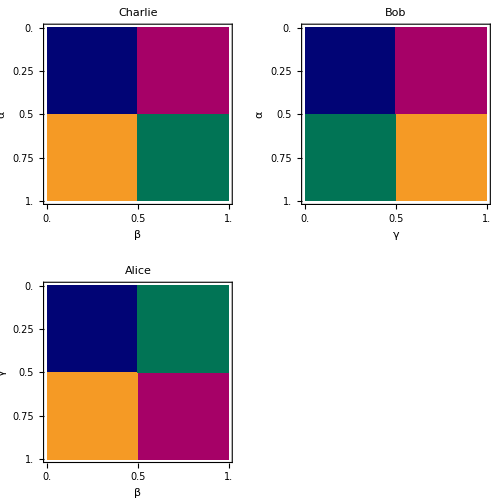
Flags:  -Graphics-

```mathematica
Module[{alice,bob,charlie,p},
alice[β_,γ_]:=If[β<=1/2,
If[γ<=1/2,1,3],
If[γ<=1/2,4,2]
];
bob[γ_,α_]:=If[γ<=1/2,
If[α<=1/2,1,4],
If[α<=1/2,2,3]
];
charlie[α_,β_]:=If[β<=1/2,
If[α<=1/2,1,3],
If[α<=1/2,2,4]
];

p=flagToDistrib[alice,bob,charlie];
echoDistrib[p];
echoFullSymmetry[p];
plotFlags[alice,bob,charlie];

];
```

## Figure 6 These flags reproduce the two-party marginals of the EJM distribution.

p =   0.0625[111] + 0.015625[113] + 0.03125[114] + 0.03125[122] + 0.015625[124] + 0.015625[131] + 0.015625[132] + 0.015625[133] + 0.03125[141] + 0.015625[143] + 0.03125[212] + 0.015625[213] + 0.03125[221] + 0.0625[222] + 0.015625[224] + 0.03125[233] + 0.015625[234] + 0.015625[241] + 0.015625[242] + 0.015625[244] + 0.015625[311] + 0.015625[313] + 0.015625[314] + 0.015625[321] + 0.03125[323] + 0.015625[331] + 0.03125[332] + 0.0625[333] + 0.015625[342] + 0.03125[344] + 0.03125[411] + 0.015625[412] + 0.015625[422] + 0.015625[423] + 0.015625[424] + 0.015625[431] + 0.03125[434] + 0.015625[442] + 0.03125[443] + 0.0625[444]

Max norm of p to full symmetry:  0.03125

pAB =   0.109375[11] + 0.046875[12] + 0.046875[13] + 0.046875[14] + 0.046875[21] + 0.109375[22] + 0.046875[23] + 0.046875[24] + 0.046875[31] + 0.046875[32] + 0.109375[33] + 0.046875[34] + 0.046875[41] + 0.046875[42] + 0.046875[43] + 0.109375[44]

pAC =   0.109375[11] + 0.046875[12] + 0.046875[13] + 0.046875[14] + 0.046875[21] + 0.109375[22] + 0.046875[23] + 0.046875[24] + 0.046875[31] + 0.046875[32] + 0.109375[33] + 0.046875[34] + 0.046875[41] + 0.046875[42] + 0.046875[43] + 0.109375[44]

pBC =   0.109375[11] + 0.046875[12] + 0.046875[13] + 0.046875[14] + 0.046875[21] + 0.109375[22] + 0.046875[23] + 0.046875[24] + 0.046875[31] + 0.046875[32] + 0.109375[33] + 0.046875[34] + 0.046875[41] + 0.046875[42] + 0.046875[43] + 0.109375[44]

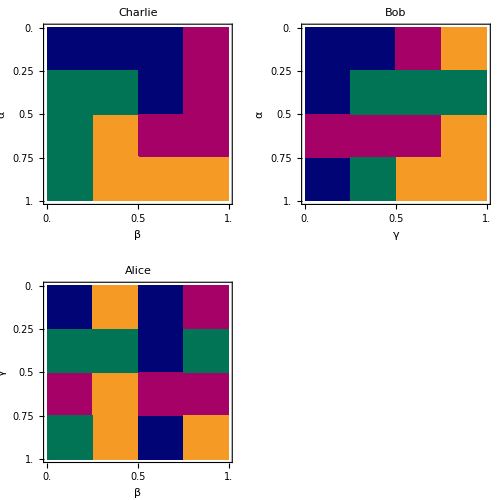
Flags:  -Graphics-

```mathematica
Module[{alice,bob,charlie,p},
alice[β_,γ_]:=Piecewise[{
{Piecewise[{{1,γ<=1/4},{2,2/4<=γ<=3/4}},4],β<=1/4},
{Piecewise[{{4,1/4<=γ<=2/4}},3],β<=2/4},
{Piecewise[{{2,2/4<=γ<=3/4}},1],β<=3/4}},
Piecewise[{{4,1/4<=γ<=2/4},{3,3/4<=γ}},2]
];
bob[γ_,α_]:=Piecewise[{
{Piecewise[{{2,2/4<=α<=3/4}},1],γ<=1/4},
{Piecewise[{{1,α<=1/4},{2,2/4<=α<=3/4}},4],γ<=2/4},
{Piecewise[{{4,1/4<=α<=2/4},{3,3/4<=α}},2],γ<=3/4}},
Piecewise[{{4,1/4<=α<=2/4}},3]
];
charlie[α_,β_]:=Piecewise[{
{Piecewise[{{1,α<=1/4}},4],β<=1/4},
{Piecewise[{{1,α<=1/4},{4,α<=2/4}},3],β<=2/4},
{Piecewise[{{1,α<=2/4},{2,α<=3/4}},3],β<=3/4}},
Piecewise[{{2,α<=3/4}},3]
];

p=flagToDistrib[alice,bob,charlie];
echoDistrib[p];
echoFullSymmetry[p];
echoTwoPartyMarginals[p];
plotFlags[alice,bob,charlie];

];
```

## Figure 9 The most general class of symmetric flags that we found.

q =  1/2

The range of q is ok:  True

Normalization of p =  1.

Max norm of p to full symmetry:  6.93889×10^-18

(s111,s112,s123) =  {0.125,0.75,0.125}

Expected:

(s111,s112,s123) =  {0.125,0.75,0.125}

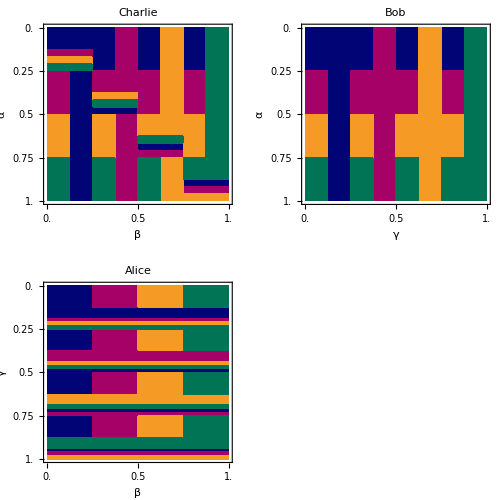
Flags:  -Graphics-

```mathematica
Module[{aliceSubflags,bobSubflags,charlieSubflags,q,r,ν,η},

aliceSubflags=Table[With[{i=i,j=j},
Piecewise[{
{Piecewise[
{{j,#2<=1-ν+η*ν},
{1+Mod[j,4],#2<=1-ν+η*ν+(1*(1-η)*ν)/3},
{1+Mod[1+j,4],#2<=1-ν+η*ν+(2*(1-η)*ν)/3}},
1+Mod[2+j,4]],
1-ν<=#2}},
i
]&],{i,4},{j,4}
];

bobSubflags:=Table[With[{i=i,j=j},
Piecewise[{
{i,#1>=1-ν}},
j
]&
],{i,4},{j,4}];

charlieSubflags:=Table[With[{i=i,j=j},
Piecewise[{
{
Piecewise[{
{i,#1<=r},
{1+Mod[i,4],#1<=r+(1*(1-r))/3},
{1+Mod[1+i,4],#1<=r+(2*(1-r))/3}
},
1+Mod[2+i,4]
],
i==j
}},
Piecewise[{
{i,#2<=1/2&&#1<=2q},
{j,#2>=1/2&&#1<=2q},
{Indexed[smallestNotEqual,{i,j}],#2<=1/2&&#1>=2q}},
Indexed[biggestNotEqual,{i,j}]
]
]&],{i,4},{j,4}];

(*Here can choose the values of r,ν,η at will.*)
Block[{q=(1-r)/3+ν/(1-ν)*(4η-1)/3,r=1/2,ν=1/2,η=1/2},
Echo[q,"q ="];
Echo[0<=q<=1/2,"The range of q is ok:"];

p=subflagsToDistrib[aliceSubflags,bobSubflags,charlieSubflags,4,4];
Echo[Sum[p[[a]][[b]][[c]],{a,4},{b,4},{c,4}],"Normalization of p ="];
echoFullSymmetry[p];
Echo[{4p[[1]][[1]][[1]],36p[[1]][[1]][[2]],24p[[1]][[2]][[3]]},"(s111,s112,s123) ="];
Echo["","Expected:"];
Echo[N/@{1/4*((1−ν)r+η*ν),3/4*((1−ν)*(1−r)+3η*ν),1/4*(1+(1−ν)*2r+(3−10η)ν)},"(s111,s112,s123) ="];

plotFlags@@(subflagsToFlag[#,4]&)/@{aliceSubflags,bobSubflags,charlieSubflags};
];

];
```

## Figure 10 Even more anti-correlated flags. Warning: the evaluation of this cell takes on the order of 5min.

Normalization of p =  1.

Max norm of p to full symmetry:  1.38778×10^-17

(s111,s112,s123) =  {0.00694444,0.229167,0.763889}

Expected:

(s111,s112,s123) =  {0.00694444,0.229167,0.763889}

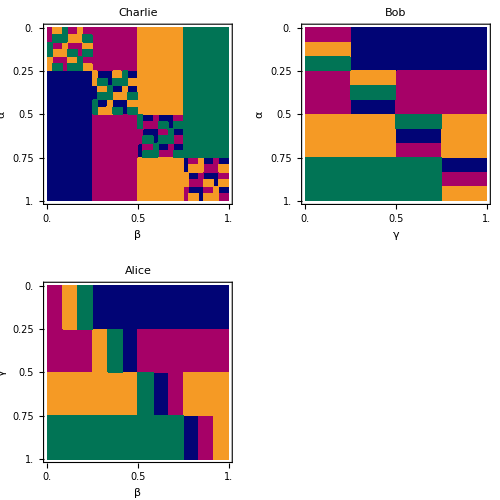
Flags:  -Graphics-

```mathematica
Module[{aliceSubflags,bobSubflags,charlieSubflags,r,subColors},

aliceSubflags=Table[With[{i=i,j=j},
Piecewise[{
{
Piecewise[
{{1+Mod[j,4],#1<=1/3},
{1+Mod[j+1,4],#1<=2/3}},
1+Mod[j+2,4]
],
i==j
}},
j
]&],{i,4},{j,4}
];

bobSubflags:=Table[With[{i=i,j=j},
Piecewise[{
{
Piecewise[
{{1+Mod[j,4],#2<=1/3},
{1+Mod[j+1,4],#2<=2/3}},
1+Mod[j+2,4]
],
i==j
}},
j
]&],{i,4},{j,4}
];

subColors={
({{2, 4, 3}, {4, 3, 2}, {3, 2, 4}}),
({{3, 1, 4}, {1, 4, 3}, {4, 3, 1}}),
({{4, 2, 1}, {2, 1, 4}, {1, 4, 2}}),
({{1, 3, 2}, {3, 2, 1}, {2, 1, 3}})
};


charlieSubflags:=Table[With[{i=i,j=j},
If[i==j,
With[{k=1+IntegerPart[3*#1],l=1+IntegerPart[3*#2]},
Piecewise[{
{Indexed[subColors,{i,k,l}],3*#2-IntegerPart[3*#2]<=r},
{Indexed[smallestNotEqual,{i,Indexed[subColors,{i,k,l}]}],3*#1-IntegerPart[3*#1]<=1/2}},
Indexed[biggestNotEqual,{i,Indexed[subColors,{i,k,l}]}]
]
]
,j]&
],{i,4},{j,4}
];

(*Here can set r to any value in [0,1]*)
Block[{r=1/3},
p=subflagsToDistribSmartDivide[aliceSubflags,bobSubflags,charlieSubflags];
Echo[Sum[p[[a]][[b]][[c]],{a,4},{b,4},{c,4}],"Normalization of p ="];
echoFullSymmetry[p];
Echo[{4p[[1]][[1]][[1]],36p[[1]][[1]][[2]],24p[[1]][[2]][[3]]},"(s111,s112,s123) ="];
Echo["","Expected:"];
Echo[N/@{r/48,(4-r)/16,(18+r)/24},"(s111,s112,s123) ="];

plotFlags@@(subflagsToFlag[#,4]&)/@{aliceSubflags,bobSubflags,charlieSubflags};
];

];
```

## Figure 14 A three-outcome strategy that violates the bound of s111 <= 1/3

Normalization of p =  1.

Max norm of p to full symmetry:  0.

(s111,s112,s123) =  {0.388889,0.388889,0.222222}

Expected:

(s111,s112,s123) =  {0.388889,0.388889,0.222222}

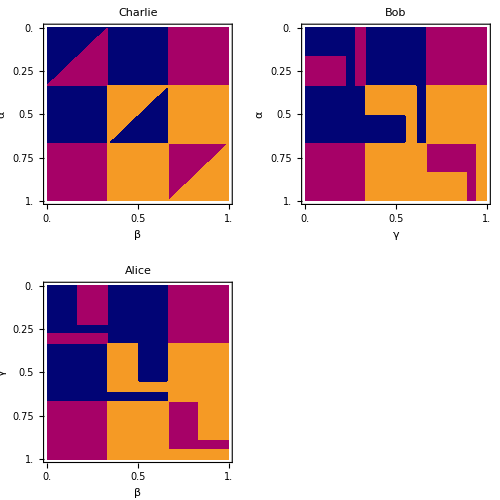
Flags:  -Graphics-

```mathematica
Module[{aliceSubflags,bobSubflags,charlieSubflags,offDiagColors,diagColors},
offDiagColors=({{0, 1, 2}, {1, 0, 3}, {2, 3, 0}});
diagColors={{1,3,2},{2,1,3}};

aliceSubflags=Table[With[{i=i,j=j},
If[i==j,
Piecewise[{
{diagColors[[1,i]],#1<=1/2&&#2<=2/3},
{diagColors[[2,i]],#1>=1/2&&#2<=2/3},
{diagColors[[1,i]],#2<=5/6}},
diagColors[[2,i]]
],
offDiagColors[[i,j]]
]&
],{i,3},{j,3}
];

bobSubflags:=Table[With[{i=i,j=j},
If[i==j,
Piecewise[{
{diagColors[[1,i]],#2<=1/2&&#1<=2/3},
{diagColors[[2,i]],#2>=1/2&&#1<=2/3},
{diagColors[[1,i]],#1<=5/6}},
diagColors[[2,i]]
],
offDiagColors[[i,j]]
]&
],{i,3},{j,3}
];

charlieSubflags:=Table[With[{i=i,j=j},
If[i==j,
If[#1+#2<=1,
diagColors[[1,i]],
diagColors[[2,i]]
],
offDiagColors[[i,j]]
]&
],{i,3},{j,3}
];

p=subflagsToDistrib[aliceSubflags,bobSubflags,charlieSubflags,3,3];
Echo[Sum[p[[a]][[b]][[c]],{a,3},{b,3},{c,3}],"Normalization of p ="];
echoFullSymmetry[p];
Echo[{3p[[1]][[1]][[1]],18p[[1]][[1]][[2]],6p[[1]][[2]][[3]]},"(s111,s112,s123) ="];
Echo["","Expected:"];
Echo[N/@{7/18,7/18,4/18},"(s111,s112,s123) ="];

plotFlags@@(subflagsToFlag[#,3]&)/@{aliceSubflags,bobSubflags,charlieSubflags};

];
```